# Get r0ket T16B0 timer interrupt sequences

## Clock frequency calculation

Clock frequency

```mathematica
fclk=72. 10^6
```

7.2×10^7

Sampling period

```mathematica
ts=100. 10^-6/16
```

6.25×10^-6

Samples per period

```mathematica
fclk ts
```

450.

```mathematica
450/5
```

90

## Get sequences

### Load file

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["r0ketIRQpr44tc9.csv"]]
```

{1048578,3}

```mathematica
Take[raw,5]
```

{{X,CH1,},{Second,Volt,},{0.0282704,-0.04,},{0.0282704,-0.04,},{0.0282704,-0.04,}}

### Extract filtered time series

```mathematica
Dimensions[timeseries=Most/@Drop[raw,2]]
```

{1048576,2}

The time information is inaccurate ⇒ compute the sampling time over the entire time series

```mathematica
ts=(First[Last[timeseries]]-First[First[timeseries]])/(Length[timeseries]-1)
```

1.×10^-8

Get voltages for digitization

```mathematica
#[Last/@timeseries]&/@{Mean,Max,Min}
```

{0.369121,2.8,-0.12}

### Digitize time series

It turns out that there is ringing on the signal, so low pass filter it with a moving 5 sample average.

```mathematica
Dimensions[dig=ListConvolve[{1,1,1,1,1}/5,Last/@timeseries]]
```

{1048572}

Add time information to filtered series again

```mathematica
Dimensions[digitized=Transpose[{ts Range[0,Length[#]-1],HeavisideTheta[#-1.00002]&/@#}]&[dig]]
```

{1048572,2}

## Analyze time series

### Run length encode time series

```mathematica
Dimensions[runs=SplitBy[digitized,Last]]
```

{3355}

```mathematica
Dimensions[runlengths={First[First[#]],Length[#]}&/@runs]
```

{3355,2}

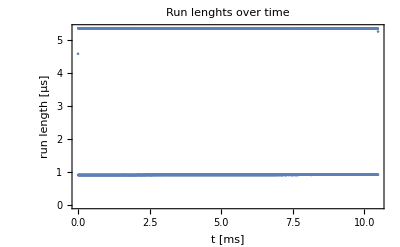

```mathematica
ListPlot[{10^3,10^6 ts}#&/@runlengths,Frame->True,PlotRange->All,FrameLabel->{"t [ms]","run length [μs]"},PlotLabel->"Run lenghts over time"]
```

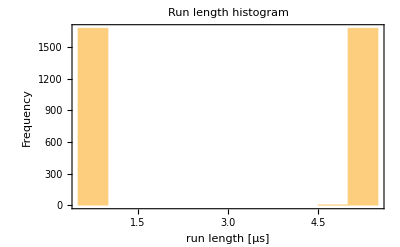

```mathematica
Histogram[10^6 ts Last/@runlengths,PlotRange->All,Frame->True,FrameLabel->{"run length [μs]","Frequency"},PlotLabel->"Run length histogram"]
```

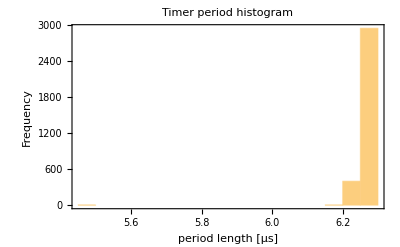

```mathematica
Histogram[ListConvolve[10^6 ts{1,1},Last/@runlengths],PlotRange->All,Frame->True,FrameLabel->{"period length [μs]","Frequency"},PlotLabel->"Timer period histogram"]
```

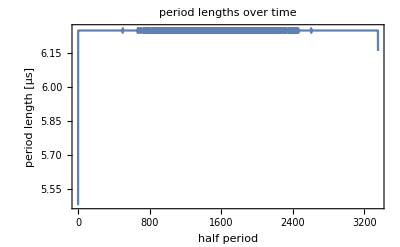

```mathematica
ListPlot[ListConvolve[10^6 ts{1,1},Last/@runlengths],PlotRange->All,Frame->True,Joined->True,FrameLabel->{"half period","period length [μs]"},PlotLabel->"period lengths over time"]
```

#### Mean period length

```mathematica
N[Mean[ListConvolve[10^6 μs ts{1,1},Last/@runlengths]]]
```

6.24977 μs

#### Period length standard deviation

```mathematica
N[StandardDeviation[10^9 ts ListConvolve[{1,1},Last/@runlengths]]]ns
```

14.248 ns

#### Longest period length

```mathematica
Max[ListConvolve[10^6 ts{1,1},Last/@runlengths]]μs
```

6.26003 μs

#### Shortest period length

```mathematica
Min[ListConvolve[10^6 ts{1,1},Last/@runlengths]]μs
```

5.48003 μs

```mathematica
Dimensions[runlengths]
```

{3355,2}

### Interrupt handling and non-interrupt handling time

```mathematica
Dimensions[irqtimes=Select[runlengths,10^6 ts Last[#]<2&]]
```

{1677,2}

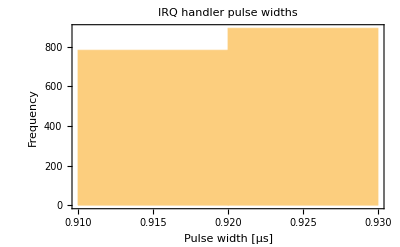

```mathematica
Histogram[10^6 ts Last[#]&/@irqtimes,Frame->True,PlotRange->All,FrameLabel->{"Pulse width [μs]","Frequency"},PlotLabel->"IRQ handler pulse widths"]
```

```mathematica
Mean[Last/@irqtimes]1.μs
```

91.5331 μs

```mathematica
Min[Last/@irqtimes]μs
```

91 μs

```mathematica
Max[Last/@irqtimes]μs
```

92 μs

```mathematica
Dimensions[nonirqtimes=Select[runlengths,10^6 ts Last[#]≥2&]]
```

{1678,2}

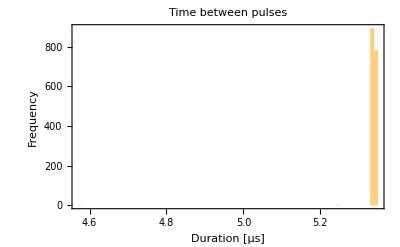

```mathematica
Histogram[10^6 ts Last[#]&/@nonirqtimes,Frame->True,PlotRange->All,FrameLabel->{"Duration [μs]","Frequency"},PlotLabel->"Time between pulses"]
```

```mathematica
Mean[Last/@nonirqtimes]1.μs
```

533.415 μs

```mathematica
Min[Last/@nonirqtimes]μs
```

457 μs

```mathematica
Max[Last/@nonirqtimes]μs
```

534 μs